# 圆和内接三角形的面积

```mathematica
DynamicModule[{r=2,vs,oc,lineTri},vs=r RandomPoint[Circle[],3];LocatorPane[Dynamic[vs,(vs=r Map[Normalize,#])&],Dynamic@Graphics[oc=TriangleCenter[vs,"Orthocenter"];
lineTri=Append[vs,First@vs];
ps=Table[v[[1]]+v[[2]]-oc,{v,Partition[lineTri,2,1]}];
oc2=TriangleCenter[ps,"Orthocenter"];{{Circle[{0,0},r]},{Purple,Thick,Line[lineTri]},{Orange,Thick,Dashed,Line[Riffle[lineTri,ps]]},{Orange,Thick,Dashed,Line[{#,oc}&/@vs]},{Orange,Thick,Dashed,Line[{#,oc2}&/@ps]},
{Magenta,PointSize[Large],Point[vs]},{Black,PointSize[Medium],Point[ps]},{PointSize[Large],Point[oc]}}],
Appearance->None]]
```

```mathematica
?*Matrix*
```

```mathematica
Partition
```

Partition

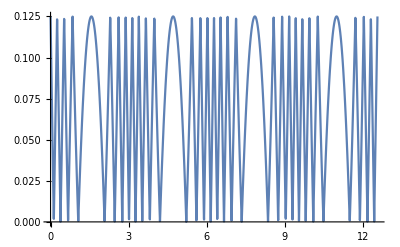

```mathematica
Plot[Abs[Abs[Abs[Abs[Sin[x]]-0.5]-0.25]-0.125],{x,0,4π}]
```

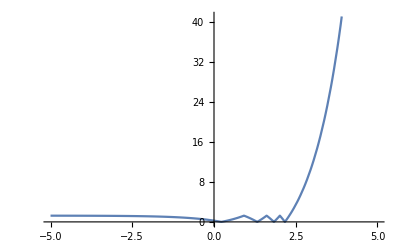

```mathematica
Plot[Abs[Abs[Abs[Exp[x]-5]-2.5]-1.25],{x,-5,5}]
```

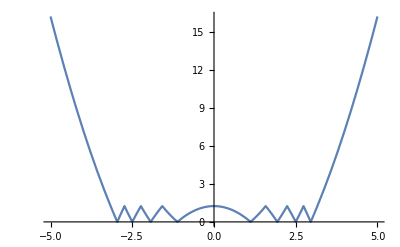

```mathematica
Plot[Abs[Abs[Abs[x^2-5]-2.5]-1.25],{x,-5,5}]
```